# Report Project 3

Course code: IX1500 - Discrete Mathematics
Date: 2017-10-10

Xing Guan, xguan@kth.se

Task 1a: Routing

## Summary

### Task

Relations between cities can be illustrated. Let us assume that each city represents a router that forwards data packets to their final destination. My task this time is to create a tree that shows how data packets are routed so that each city can be reached by the information flow that (this time) is based on Stockholm.

### Result

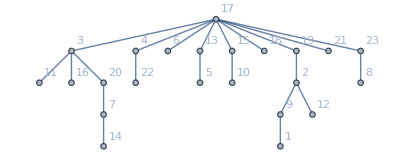
Using the built-in method FindShortestPath[graph, start, destination], the information flow is easily found. The start is always Stockholm and destination all other cities. The result can be represent as the shortest path spanning tree in the tree below.
-Graphics-

## Cost and routing

### Set the weight of edge between cities

First of all, the weight or cost of a link between two cities is inversely proportional to the  free capacity of the link. In this case the weight is set up as table below.

City1 | City2 | Free capacity
Stockholm | Göteborg | 25
Stockholm | Lund | 25
Göteborg | Lund | 25
Stockholm | Falun | 15
Falun | Östersund | 15
Östersund | Umeå | 15
other city1  | other city2 | 1-5

The capacity is larger between the large cities. And for the rest of the cities in the list have a random capacity between 1 to 5.

Having a complete list of capacity we can now set the weight between the links which is inversely proportional as mentioned before. For example the weight/cost between Stockholm and Göteborg is one divide the free capacity which is 1/25. The weight between cities that are not mentioned will vary between 1, 1/2, 1/3,1/4 and1/5 which also means that they are more costly than between larger cities.

The weight are setting up using the functions setWeight[cities, city1, city2] and setAllweight[cities, links] which I created. The code can be found under code section. The setWeight function give a weight based on the table above. The setAllweight function loops through all the links between cities and set weight on them.

### Finding Shortest path

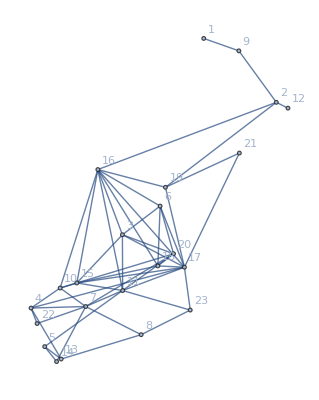
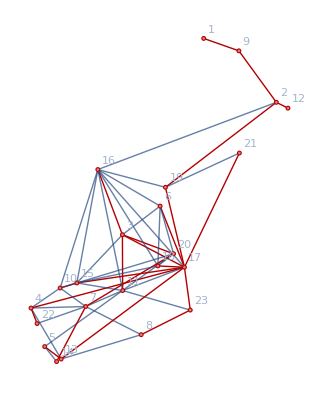
To begin with we can create a graph with cycle in it. The graph is created by the links which were given of the task instruction. Using the built-in method Graph[links,  EdgeWeight→ weights, Vertexlabels -> Automatic] we can create a graph such as the graph below. Each number represents a city. 
-Graphics-
Now we have a graph and we have set the weights between cities or in the edges. Using the built-in method FindShortestPath[graph, city1, city2] we can find all the shortest path between cities. In this case the city1 is always Stockholm and city2 is the rest of the cities. Using the all the paths which are found by FindShortestPath method we can now create a tree in the picture below. 
-Graphics-

The graph below are using the built-in method HighlightGraph[]. The highlighted graph represents the shortest path spanning tree we created and the original graph in the background.
-Graphics-


For example, call the function FindShortestPath[shortestTree,17, 1 ]. It will give the information flow which is 17 → 18 →  2 → 9 → 1 (See the tree to verify).

## Code

```mathematica
ClearAll["`*"]
$AllowInternet=True

city={"Abisko","Boden","Falun","Goteborg","Hoganas","Hudiksvall","Jonkoping","Kalmar","Kiruna","Lidkoping","Linkoping","Lulea","Lund","Malmo","Mariestad","Ostersund","Stockholm","Strangnas","Timra","Uppsala","Umea","Varberg","Visby"};

links={{15,18},{13,17},{3,16},{6,3},{18,6},{12,2},{15,11},{19,21},{7,8},{19,2},{7,4},{21,17},{17,11},{23,11},{10,7},{16,17},{10,20},{13,5},{3,17},{7,22},{15,10},{16,18},{11,16},{17,23},{18,17},{20,6},{11,7},{9,2},{3,20},{4,17},{19,17},{7,20},{22,4},{14,7},{15,17},{6,17},{20,5},{16,15},{11,3},{9,1},{4,10},{5,14},{6,16},{16,19},{13,8},{8,23},{16,10},{4,13},{2,16},{15,3},{20,18}};
```

True

```mathematica
(*input with the name of the city1,2 . t.ex links [1], ...[2] *)
setWeight [city_, cityNr1_, cityNr2_]:=
Module[{
freeCapacity
},
city1Name = city[[cityNr1]];
city2Name = city[[cityNr2]];
(*constants*)
freeCapacity = 0;
Stockholm = city[[17]];
Goteborg = city[[4]];
Lund = city[[13]];
Falun = city[[3]];
Ostersund = city[[16]];
Umea = city[[21]];
(* Special links that have more capacity *)
If[(city1Name== Stockholm ∨ city1Name == Goteborg )∧  (city2Name== Stockholm ∨ city2Name == Goteborg ),freeCapacity = 25] ;
If[(city1Name== Stockholm ∨ city1Name == Lund )∧  (city2Name== Stockholm ∨ city2Name == Lund ),freeCapacity = 25] ;
If[(city1Name== Goteborg ∨ city1Name == Lund )∧  (city2Name== Goteborg ∨ city2Name == Lund ),freeCapacity = 25] ;
If[(city1Name== Stockholm ∨ city1Name == Falun )∧  (city2Name== Stockholm ∨ city2Name == Falun ),freeCapacity = 15] ;
If[(city1Name== Falun ∨ city1Name == Ostersund )∧  (city2Name== Falun ∨ city2Name == Ostersund ),freeCapacity = 15] ;
If[(city1Name== Ostersund ∨ city1Name == Umea )∧  (city2Name== Ostersund ∨ city2Name == Umea ),freeCapacity = 15] ;
(* If it's small cities then set the capacity randomly between 1 to 5*)
If[freeCapacity == 0, freeCapacity = RandomInteger[{1,5}]];
freeCapacity = 1/freeCapacity;
freeCapacity
];

(* loop through all links and set weight on them *)
setAllweight[city_, links_]:=Module[{
 cityNo1, cityNo2,saveWeights,lengthLinks, temp
},
lengthLinks = Length[links];
(*just initialize the length of weights for each connection between cities*)
saveWeights  = Range[lengthLinks]; 
For[i=1,i<lengthLinks+1,i++,
cityNo1 = links[[i]][[1]];
cityNo2 = links[[i]][[2]];
(* set weight in each link *)
temp = setWeight[city, cityNo1, cityNo2];
(* set the weight on that link*)
saveWeights[[i]] = temp;
];
(*return a list of weights*)
saveWeights
];
```

```mathematica
(*find the path between Stockholm and rest of the cities*)
pathFromStockholmToRest[graph_, city_]:= Module[{
lengthCity, pathList, city1, city2, tempPath
},
lengthCity = Length[city];
pathList = {};
For[i=1,i<lengthCity+1,i++,
If[i==17,Continue[]];
city1 = 17;
city2 = i;
(* find shortest path between Stockholm and other cities *)
tempPath = FindShortestPath[graph, city1,city2];
(* append the each path to the list *)
AppendTo[pathList, tempPath];
];
(* return a list of different path from stockholm to rest of the cities *)
pathList 
];
(* Link up between the two cities, with no dublett *)
linksWithShortestPath [allList_] := Module[{
Alllinks, lengthOfAllrouter,lengthEachRouter, tempLink, reversTempLink, eachRouter
},
Alllinks = {};
lengthOfAllrouter = Length[allList];
For[i=1, i < lengthOfAllrouter+1, i++, 
eachRouter = allList[[i]];

lengthEachRouter = Length[eachRouter];
For[j = 1, j < lengthEachRouter, j++,
tempLink = {eachRouter[[j]], eachRouter[[j+1]]};
reversTempLink = {eachRouter[[j+1]], eachRouter[[j]]};
If[MemberQ[Alllinks, tempLink]  ∨ MemberQ[Alllinks, reversTempLink], Continue[], AppendTo[Alllinks, tempLink] ];
];
];
(* return all the links between cities with minimum cost *)
Alllinks
];
```

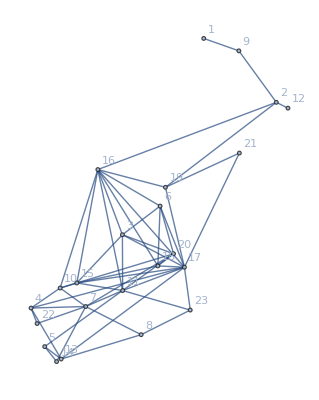

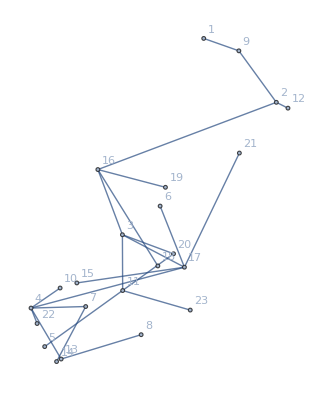

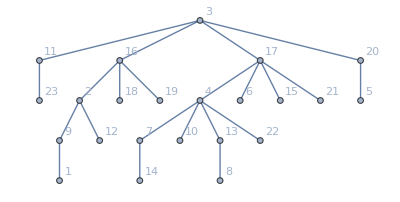

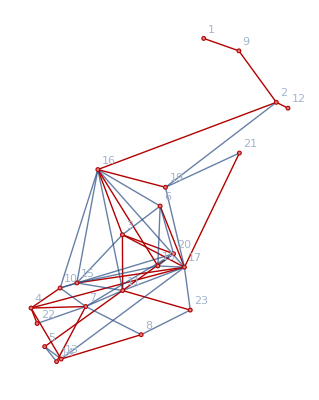

```mathematica
(*function that can retrive the coordination of a city*)
pos[c_String]:=CityData[c,"Coordinates"];
(* to get the coordinations of cities*)
c=pos/@city; (* city coordinates *)
n = Length[city]; (* length is 23 in this case *)
weights= setAllweight[city, links];(*get a list of weights*)
(*with link between Stockholm and Lund*)
originalGraph= Graph[links, EdgeWeight-> weights, VertexCoordinates->(Reverse/@c),VertexLabels-> Automatic]
(*with link between Stockholm and Lund*)
originalWithoutLund = EdgeDelete[originalGraph,13<-> 17];
allList = pathFromStockholmToRest[originalWithoutLund, city];
Alllinks  = linksWithShortestPath[allList];

treeGraph =  Graph[Alllinks, VertexCoordinates->(Reverse/@c),VertexLabels-> Automatic]

tree = Graph[Alllinks, VertexLabels-> Automatic]
(* highlight the treeGraph *)
HighlightGraph[originalGraph,treeGraph, GraphHighlightStyle->   "Thick"]
```

Task 1b: Illustrate with the map of Sweden

## Summary

### Task

Illustrate the solution with the map of Sweden and what happens if the link between Stockholm and Lund stops working?

### Result

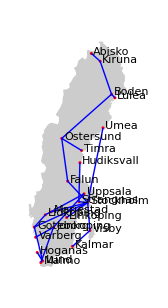
-Graphics-
(Zoom in to see a clearer map)

If the link between Stockholm and Lund stops working, we can simply find the next best tree which have all cities included but without link between those cities. The cost between Stockholm and Lund will perhaps be higher due to the tree before have more optimized cost.

## Map and illustration of routing

### Visualize the routers with map and with and without Lund-link

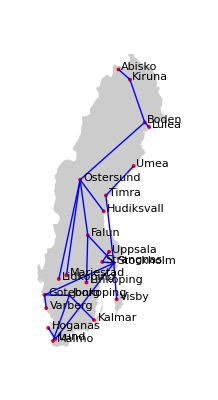
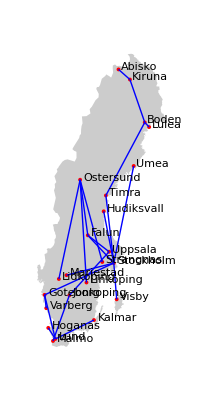
With the given function geoGraph[], we can easily illustrate the map by putting in the parameters to the function. We need the vertex/cities, edges/weights, the coordination of each city and radian which says how big the circle is to represent each city in the map(see the red dot in the map below).


-Graphics-
The map above is allowing with the edge between Stockholm and Lund. As we delete the edge using built-in method EdgeDelete[] we see that the tree’s structure is changed. It finds an another tree which direct Stockholm to Lund with other routers. We can also see that the link between Stockholm and Lund is longer and is more costly. Due to the cost before is 1/25 comparing to the cost now which is higher equal or higher than 1/5.
-Graphics-

## Code

```mathematica
(*Graph function from the instruction*)
Options[geoGraph]={
EdgeStyle->Black,VertexStyle->GeoStyling[None],
VertexLabels->None,VertexLabelStyle->Black
};
geoGraph[v_,e_,c_,r_,OptionsPattern[]]:=
Module[{
es=OptionValue[EdgeStyle],vs=OptionValue[VertexStyle],vl=OptionValue[VertexLabels],vls=OptionValue[VertexLabelStyle],
lbl,Δ={0.1,0.3}
},
If[Length[vl]≠Length[v],vl=None];
lbl=If[
vl===None,{},
Join[{vls},MapThread[Text[#1,GeoPosition[#2+Δ],{-1,0}]&,{vl,c}]]
];
Join[
Join[{vs},(GeoDisk[c⟦#1⟧,r]&)/@v],
Join[{es},(GeoPath[{c⟦#1⟦1⟧⟧,c⟦#1⟦2⟧⟧}]&)/@e],
lbl
]
];
```

{17<->3,3<->16,16<->2,2<->9,9<->1,17<->4,3<->20,20<->5,17<->6,4<->10,10<->7,4<->13,13<->8,16<->15,15<->11,2<->12,5<->14,17<->18,17<->19,19<->21,4<->22,11<->23}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23}

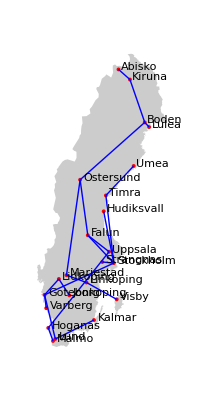

```mathematica
(* Illustrate the routers with map from Sweden *)
𝔈=EdgeList[treeGraph]
𝔙=VertexList[treeGraph]
r=10×10^3;
(* in this case it is the map without link between Lund and Stockholm *)
GeoGraphics[{
Polygon[CountryData["Sweden"]],
geoGraph[𝔙,𝔈,c,r,EdgeStyle->Blue,VertexStyle->GeoStyling[Red],VertexLabels->city]
},GeoBackground->None,GeoProjection->"LambertAzimuthal"]
```